## Plotting phase diagrams with numerically solved cavity equations

created by Zhijie Feng,  contact: zjfeng@bu.edu

In this notebook, we demonstrate how we solve cavity equation numerically in the paper “Emergent competition shapes the ecological properties of multi-trophic ecosystems”. Here we plot the phase diagrams to study the effect of parameters including r_1, r_2, k, u.

### Define functions for Gaussian integrals

Here we define the integrals for the 0, 1 and 2nd moment of truncated Gaussians  as functions. We directly use the result from Integration in terms of error function speed up the code.

```mathematica
w0[d_]:=1/2 (1+Erf[d/(√2)])
w1[d_]:=(ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))/(√(2 π))
W[d_]:=((ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))^2)/(√(2 π) (d ⅇ^(-d^2/2)+(1+d^2) √(π/2) (1+Erf[d/(√2)])))
```

```mathematica
(*here just to demonstrate these are indeed the integration result*)
Simplify[w0[d]-Integrate[1/Sqrt[2 Pi]Exp[-x^2/2],{x,-d,Infinity}]] (*w0=zeroth moment*)
Simplify[w1[d]-Integrate[1/Sqrt[2 Pi](x+d)Exp[-x^2/2],{x,-d,Infinity}]] (*w1=first moment*)
Simplify[w1[d]^2/W[d]-Integrate[1/Sqrt[2 Pi](x+d)^2Exp[-x^2/2],{x,-d,Infinity}]](*(W=w1^2/w2 for simplification*)
```

0

0

0

### Fixed model parameters , and define solver

We define the solver for self consistency equations from cavity method. The parameters r1, r2 and k are varied while others are all fixed.

```mathematica
sigmau=0.1;
sigmam=0.1;
sigmak=0.1;
m=1;
muc=1;
mud=1;

Simulate[r1_,r2_,kvar_,uvar_,sigmacvar_,sigmadvar_](*small system ODE simulation to obtain good initial guess*):=Module[{},k=kvar; u=uvar;sigmac=sigmacvar;
sigmad=sigmadvar;
topspecies=20;
middlespecies=Round[topspecies/r1];
resources=Round[topspecies/r1/r2];

tfinal=10;

iniX=RandomReal[{1,2},{topspecies}];
inin=RandomReal[{1,2},{middlespecies}];
iniR=RandomReal[{1,2},{resources}];

Dm=RandomVariate[NormalDistribution[mud/middlespecies,sigmad/Sqrt[middlespecies]],{topspecies,middlespecies}];
Cm=RandomVariate[NormalDistribution[muc/resources,sigmac/Sqrt[resources]],{middlespecies,resources}];
us=RandomVariate[NormalDistribution[u,sigmau],topspecies];
ms=RandomVariate[NormalDistribution[m,sigmam],middlespecies];
ks=RandomVariate[NormalDistribution[k,sigmak],resources];
eqns={X'[t]==X[t](Dm.n[t]-us),n'[t]==n[t](Cm.R[t]-ms-Transpose[Dm].X[t]),R'[t]==R[t](ks-R[t]-Transpose[Cm].n[t]),X[0]==iniX,n[0]==inin,R[0]==iniR};
solution=NDSolve[eqns,{X,n,R},{t,tfinal},Method->"StiffnessSwitching"][[1]];
Rmean=Evaluate[Mean[R[tfinal]]/.solution];
Nmean=Evaluate[Mean[n[tfinal]]/.solution];
Xmean=Evaluate[Mean[X[tfinal]]/.solution];

Rq=Evaluate[(Mean[R[tfinal]^2])/.solution];
Nq=Evaluate[(Mean[n[tfinal]^2])/.solution];
Xq=Evaluate[(Mean[X[tfinal]^2])/.solution];

{Rmean,Nmean,Xmean,Rq,Nq,Xq}
]


Wholesolve[r1_,r2_,kvar_,uvar_,sigmacvar_,sigmadvar_](*Here we define the solver for cavity equations*):={
k=kvar;
u=uvar;
sigmac=sigmacvar;
sigmad=sigmadvar;

Sigmaue[qn_]:=Sqrt[sigmad^2 qn+sigmau^2];
Sigmame[qr_,qx_]:=Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Sigmake[qn_]:=Sqrt[sigmak^2+sigmac^2r2 qn ];

Deltaue[qn_,n_]:=-(u-mud  n)/Sqrt[sigmad^2 qn+sigmau^2];
Deltame[x_,R_,qx_,qr_]:=-(m+r1 mud x-muc R)/Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Deltake[n_,qn_]:=(k-muc r2 n)/Sqrt[sigmak^2+sigmac^2r2 qn ];

simulated=Simulate[r1,r2,kvar,uvar,sigmacvar,sigmadvar];


deltaue=Deltaue[qn,n];
deltame=Deltame[x,R,qx,qr];
deltake=Deltake[n,qn];
sigmaue=Sigmaue[qn];
sigmame=Sigmame[qr,qx];
sigmake=Sigmake[qn];

sus=Solve[{0==X-w0[deltaue]/(sigmad^2 V),0==V+ w0[deltame]/(sigmac^2Ka-r1 sigmad^2 X),0==Ka-w0[deltake]/(1-r2 sigmac^2 V)},{X,V,Ka}][[1]];

Fullfunction={x+sigmaue/(sigmad^2V+0.000000000000000000001) w1[deltaue],n-sigmame/(sigmac^2 Ka-r1 sigmad^2 X+0.000000000000000000001) w1[deltame],R-sigmake/(1-r2 sigmac^2 V+0.000000000000000000001)w1[deltake],
qx-x^2/W[deltaue],
qn-n^2/W[deltame],
qr-R^2/W[deltake]}/.sus;(*Here are the 6 self-consistent equations to be solved, a very small value is added in the demoninator to reduce the chance of numerical explosion*)

{x,qx,R,qr,n,qn,w0[deltaue],w0[deltame],w0[deltake]}/.
NMinimize[{Fullfunction.Fullfunction,{R>0&&n>0&&x>0&&qr>0&&qn>0&&qx>0&&-w0[Deltaue[qn,n]]+1/r1*w0[Deltame[x,R,qx,qr]]>0&&w0[Deltaue[qn,n]]+1/r1 *1/r2 *w0[Deltake[n,qn]]-1/r1 *w0[Deltame[x,R,qx,qr]]>0}},{{R,simulated[[1]]/2,simulated[[1]]},{n,simulated[[2]]/2,simulated[[2]]},{x,simulated[[3]]/2,simulated[[3]]},{qr,simulated[[4]]/2,simulated[[4]]},{qn,simulated[[5]]/2,simulated[[5]]},{qx,simulated[[6]]/2,simulated[[6]]}},AccuracyGoal->6,MaxIterations->30000][[2]]}[[1]] (*the range for initial solution guessing is determined by simulation result of a small system*)
Wholesolve[0.4,0.4,1,5,2.5,2.5]
```

{1.31367×10^-13,5.35048×10^-25,0.769169,0.707127,0.14186,0.0676869,7.76601×10^-14,0.456333,0.987064}

### Evaluate solution for a range of parameters and save the result

Here we set the range of parameters to evaluate the cavity equations. Slight change in this section

```mathematica
r1start=0.4;
r1end=1.2;
r1interval=(r1end-r1start)/1;
r1list=N[Range[r1start,r1end,r1interval]];

r2start=0.4;
r2end=1.2;
r2interval=(r2end-r2start)/1;
r2list=N[Range[r2start,r2end,r2interval]];

sigmac=0.5;
sigmad=0.5;
numsigmac=1;
numsigmad=1;

(*to vary sigmas, delete the above 4 lines and uncomment the code below *)

(*sigmastart=1;
sigmaend=2.5;
sigmainterval=(sigmaend-sigmastart)/5;
sigmalist=N[Range[sigmastart,sigmaend,sigmainterval]];
numsigmac=Length[sigmalist];
numsigmad=Length[sigmalist];*)

kstart=1;
kend=5;
kinterval=(kend-kstart)/10;
klist=N[Range[kstart,kend,kinterval]];


ustart=1;
uend=3;
uinterval=(uend-ustart)/10;
ulist=N[Range[ustart,uend,uinterval]];


Allsolutionku=ParallelTable[Wholesolve[r1,r2,k,u,sigmac,sigmad],{r1,r1start,r1end,r1interval},{r2,r2start,r2end,r2interval},{k,kstart,kend,kinterval},{u,ustart,uend,uinterval}];

(*to vary sigmas, delete the above line and uncomment the code below *)
(*Allsolutionsigmas=ParallelTable[Wholesolve[r1,r2,k,u,sigmac,sigmad],{r1,r1start,r1end,r1interval},{r2,r2start,r2end,r2interval},{k,kstart,kend,kinterval},{u,ustart,uend,uinterval},{sigmac,sigmastart,sigmaend,sigmainterval},{sigmad,sigmastart,sigmaend,sigmainterval}];
```

### Get the effective competition and order parameters from the solutions

In the paper, we derived the emergent competition D_eff^X,  D_eff^N,  D_eff^R , and the order parameter D_eff^(N, top)/ D_eff^(N, bottom)

```mathematica
GetDtopbottom[r1_,r2_,Allsolutionku_]:={g=Allsolutionku[[All,All,9]]/r1/r2;
b=Allsolutionku[[All,All,8]]/r1;
w=Allsolutionku[[All,All,7]];
(w/b)/(1-w/b)}

GetDeff[r1_,r2_,Allsolutionku_]:=
{g=Allsolutionku[[All,All,9]]/r1/r2;
b=Allsolutionku[[All,All,8]]/r1;
w=Allsolutionku[[All,All,7]];
f=(g)/(b-w)-1;
phiN=Allsolutionku[[All,All,8]];

{DXeff=sigmad^2/sigmac^2/f/r2,
DNeff=phiN sigmac^2f r2,
DReff=1+1/f}
}

AllDtopbottom=Table[GetDtopbottom[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1]],{r1index,1,2,1},{r2index,1,2,1}];
AllDX=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,1]],{r1index,1,2,1},{r2index,1,2,1}];
AllDN=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,2]],{r1index,1,2,1},{r2index,1,2,1}];
AllDR=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,3]],{r1index,1,2,1},{r2index,1,2,1}];
```

### Plotting the phase diagrams

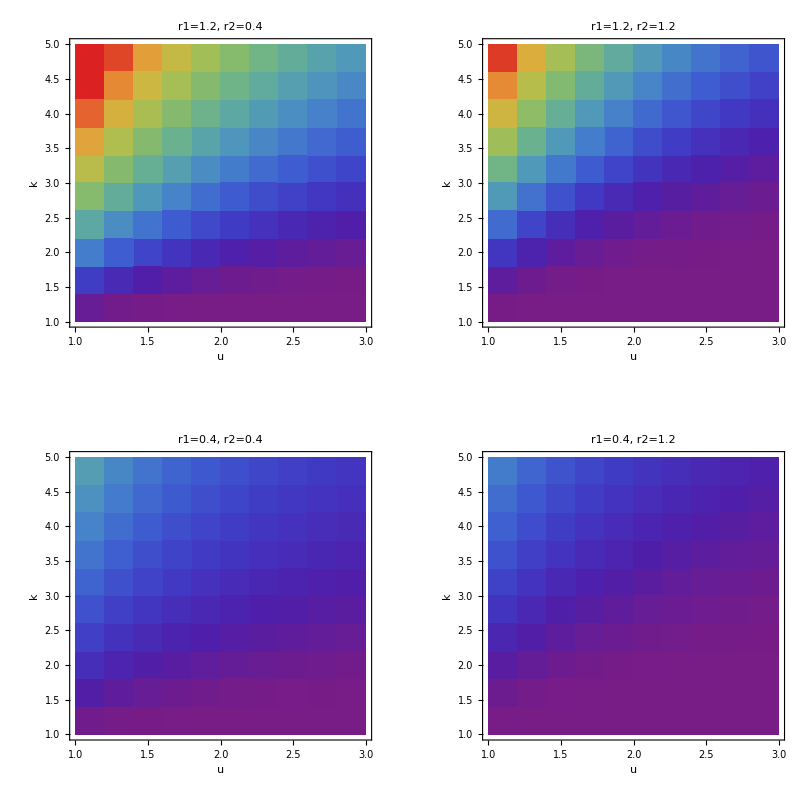

```mathematica
opts1={InterpolationOrder->0,DataRange->{{1,3},{1,5}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,6}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 0 to 6*)

AllFiguresku=Table[
ListDensityPlot[AllDtopbottom[[3-r1index,r2index]],Evaluate[opts1],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsGrid[AllFiguresku],PlotLabel->"Order parameter D_top/D_bottom"]
```

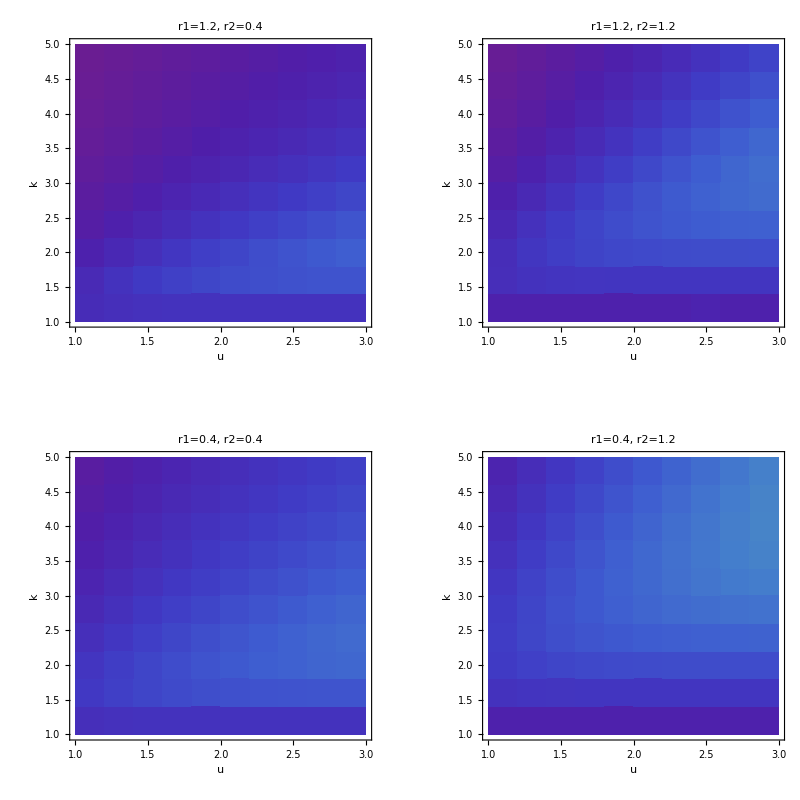

```mathematica
opts2={InterpolationOrder->0,DataRange->{{1,3},{1,5}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 1 to 3*)
AllDxku=Table[
ListDensityPlot[AllDX[[3-r1index,r2index]],Evaluate[opts2],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsGrid[AllDxku],PlotLabel->"effective competition D"]
```

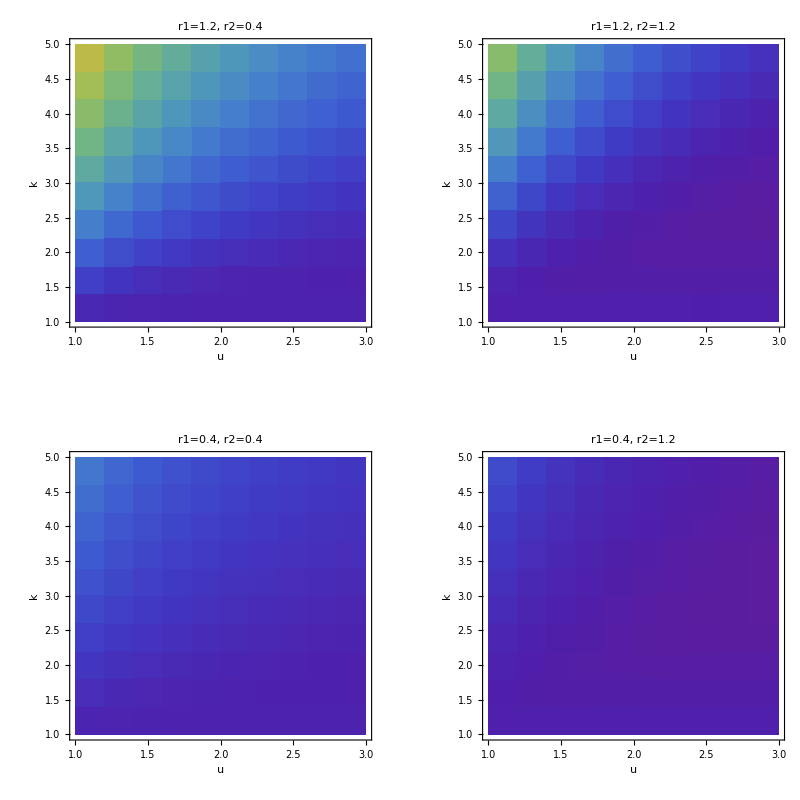

```mathematica
opts3={InterpolationOrder->0,DataRange->{{1,3},{1,5}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 1 to 3*)
AllDNku=Table[
ListDensityPlot[AllDN[[3-r1index,r2index]],Evaluate[opts3],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsGrid[AllDNku],PlotLabel->"effective competition D"]
```

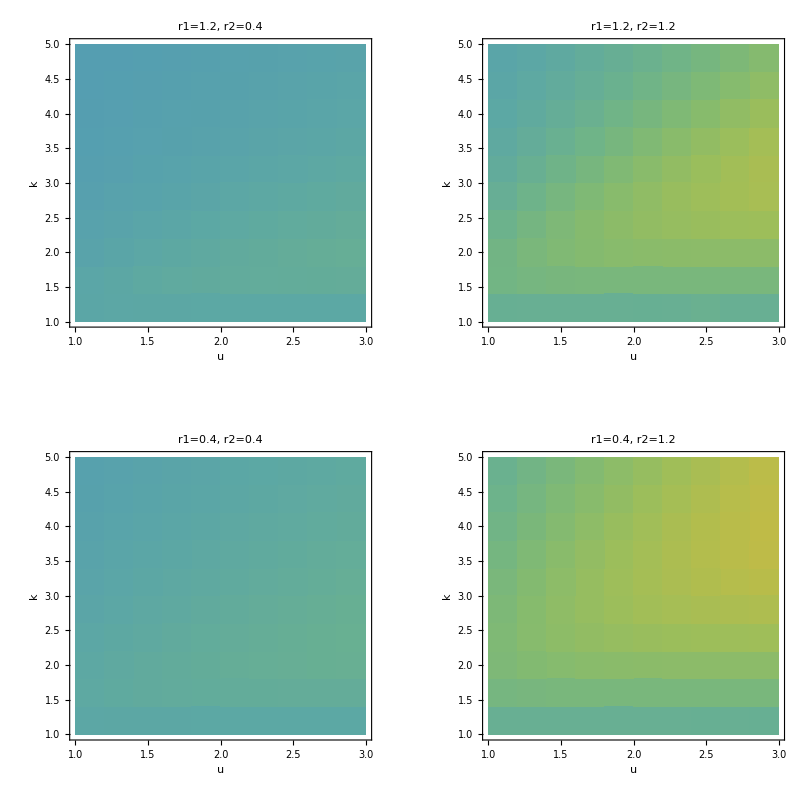

```mathematica
opts4={InterpolationOrder->0,DataRange->{{1,3},{1,5}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"}};(*here we fixed the color scale for all four diagrams to value 0 to 3*)
AllDRku=Table[
ListDensityPlot[AllDR[[3-r1index,r2index]],Evaluate[opts4],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsGrid[AllDRku],PlotLabel->"effective competition D"]
```